```mathematica
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50."&);

thrustCurve=Import["https://pastebin.com/raw/shyR8vJp","Table"];
ifun=Interpolation[thrustCurve,InterpolationOrder->1];
Thrust[t_]=Piecewise[{{ifun[t],0<t<3.45}}];
m=1.0565;
g=9.80655;

sol=ParametricNDSolve[{s''[x]==Thrust[x]/m-g,s'[0]==vo,s[0]==so,WhenEvent[s[x]==0,If[x>3.45,"StopIntegration",s'[x]->0]]},{s,s'},{x,0,∞},{vo,so}, "ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False},AccuracyGoal-> 5,PrecisionGoal -> 5, MaxSteps->Infinity];
h=s/.%;
v=s'/.sol;
```

```mathematica
sstart = 10;
send = 20;
ds = 0.1;
vstart= -15;
vend = -7;
dv = 0.1;
velocities=ArrayReshape[Max[Abs[#'/@((t/.Table[FindRoot[#[t],{t,t0,0,#["Domain"][[1,2]]}],{t0,0.1,#["Domain"][[1,2]],#["Domain"][[1,2]]}]) -.001)]] &/@Flatten[Table[h[va,sa],{va,vstart,vend,dv}, {sa, sstart, send, ds}]], IntegerPart[{Abs[vstart -vend]/ dv + 1, Abs[sstart - send]/ ds + 1}]];
```

InterpolatingFunction::dmval: Input value {3.47037} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.74764} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {3.66027} is at the edge of the search region {0.,3.66027} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {3.70452} is at the edge of the search region {0.,3.70452} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {3.74276} is at the edge of the search region {0.,3.74276} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

```mathematica
ArrayReshape[Max[Abs[#'/@((t/.Table[FindRoot[#[t],{t,t0,0,#["Domain"][[1,2]]}],{t0,0.1,#["Domain"][[1,2]],#["Domain"][[1,2]]}]) -.00001)]] &/@Flatten[Table[h[va,sa],{va,vstart,vend,dv}, {sa, 20, 30, 1}]], IntegerPart[{Abs[vstart -vend]/ dv + 1, Abs[sstart - send]/ ds + 1}]]
```

InterpolatingFunction::dmval: Input value {3.46583} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/(1.27331×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.20715×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
vt = Range[vstart,vend,dv];
st = Range[sstart, send, ds];
velocities[[IntegerPart[Abs[vstart - -12.8]/ dv + 1], IntegerPart[Abs[sstart - 20]/ ds + 1]]]
Flatten[Table[{vt[[i]],st[[j]],velocities[[i,j]]},{i,Abs[vstart - vend]/ dv + 1},{j, Abs[sstart - send]/ ds + 1}],1];
ListPlot3D[%, AxesLabel->{v0, s0, Impact Velocity}]
```

1.7629

-Graphics3D-

ReplaceAll::reps: {InterpolatingFunction[{{0.,2.10256171382009×10^3139}},{5,19,2,{9956},{4},{1},0,0,0,Automatic,{},{},False},{{0.,«49»,«9906»}},{{92.,-34.,-9.80655},{91.9959,-34.0012,-9.80061},{91.9917,-34.0024,-9.79467},{91.9835,-34.0048,-9.78279},{91.9752,-34.0071,-9.77091},{91.9669,-34.0095,-9.75903},{91.8842,-34.0331,-9.64023},«37»,{84.2644,-34.9561,1.5188},{84.2484,-34.9554,1.54394},{84.0875,-34.9477,1.79565},{84.0553,-34.946,1.85028},{84.0231,-34.9443,1.90492},{83.9909,-34.9425,1.95956},«9906»},{Automatic}][Table[«1»,«1»]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

{{{t→0.197436},{t→7.60567}}}

{{{-50.9769,-27.0227}}}

-50.9769

InterpolatingFunction[…]

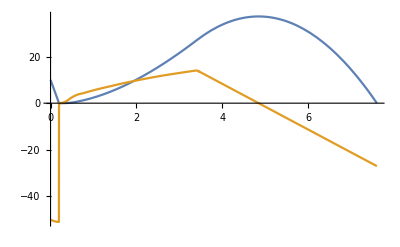

{-1,32}

```mathematica
Table[FindRoot[#[t],{t,t0,0,#["Domain"][[1,2]]}],{t0,0,#["Domain"][[1,2]],#["Domain"][[1,2]]}]&/@{h[-50,10]}
#'/@ ((t /. %)-.0001)&/@{h[-50,10]}
v[-50, 10][0.19743284]
h[-50,10]
Plot[{h[-50,10][t], v[-50,10][t]}, {t, 0, 7.62}]
```